Name: Karan Sharma
College Roll No.: 2232191
University Roll No. : 22036563079
Class: BSc (Hons) Mathematics / Year 3 / Complex Analysis
Section: A

# PRACTICAL 1 - nth roots of unity

Show that the nth roots of unity are equally spaced points that lie on the unit circle and form the vertices of a regular polygon with n sides, for n = 4, 5, 6, 7, 8

```mathematica
ClearAll
Solve[z^3==1,z]
s=N[Solve[z^3==1,z]]
(*extract the values from above solution*)
s[[3]][[1]][[2]]
s[[2,1,2]]
```

ClearAll

{{z→1},{z→-(-1)^(1/3)},{z→(-1)^(2/3)}}

{{z→1.},{z→-0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ}}

-0.5+0.866025 ⅈ

-0.5-0.866025 ⅈ

(i) n = 3

ClearAll

{{z→1.},{z→-0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ}}

1.

-0.5-0.866025 ⅈ

-0.5+0.866025 ⅈ

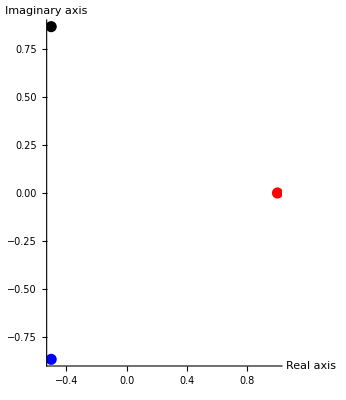

```mathematica
ClearAll
s=N[Solve[z^3==1,z]]
z1=s[[1,1,2]]
z2=s[[2,1,2]]
z3=s[[3,1,2]]
a=Graphics[
{
PointSize[0.02],Red,
Point[{Re[z1],Im[z1]}],Blue,
Point[{Re[z2],Im[z2]}],Black,
Point[{Re[z3],Im[z3]}]
}, Axes->True,AxesLabel->{"Real axis","Imaginary axis"}
]
```

```mathematica
(*b=Graphics[Circle[{0,0},1]]*)
c=PolarPlot[1,{τ,0,2π},PolarAxes->True,PolarGridLines->True];
Show[c,a]
```

-Graphics-

```mathematica
(*Write some text on the graph*)
d=Graphics[{Text["z_1",{1.1,0.05}],Text["z_2",{-0.5,-0.95}],Text["z_3",{-0.5,0.95}]}]; 
e=Graphics[{Purple,Thick,
Line[{{0,0},{Re[z1],Im[z1]}}],
Line[{{0,0},{Re[z2],Im[z2]}}],
Line[{{0,0},{Re[z3],Im[z3]}}]
}];
Show[c,a,d,e]
```

-Graphics-

```mathematica
If[Arg[z1/z2]==Arg[z2/z3]==Arg[z3/z1],Text["All the points are equally spaced"],Text["Points are not equally spaced"]]
```

All the points are equally spaced

```mathematica
f=Graphics[{Red,Thick,
Line[{{Re[z1],Im[z1]},{Re[z2],Im[z2]}}],
Line[{{Re[z1],Im[z1]},{Re[z3],Im[z3]}}],
Line[{{Re[z2],Im[z2]},{Re[z3],Im[z3]}}]}];
Show[c,a,d,e,f](*Show function displays the graphs in the order given by the user*)
```

-Graphics-

```mathematica
If[Abs[z1-z3]==Abs[z3-z2]==Abs[z1-z2],Text["The polygon is regular"], Text["The polygon is not regular"]]
```

The polygon is regular

(ii) n = 4

```mathematica
ClearAll;
s=N[Solve[z^4==1,z]]
```

{{z→-1.},{z→0.-1. ⅈ},{z→0.+1. ⅈ},{z→1.}}

```mathematica
ω1=s[[1,1,2]]
ω2=s[[2,1,2]]
ω3=s[[3,1,2]]
ω4=s[[4,1,2]]
```

-1.

0.-1. ⅈ

0.+1. ⅈ

1.

```mathematica
a=Graphics[
{
PointSize[0.02],
Red,Point[{Re[ω1],Im[ω1]}],
Blue,Point[{Re[ω2],Im[ω2]}],
Black,Point[{Re[ω3],Im[ω3]}],
Orange,Point[{Re[ω4],Im[ω4]}]
}, Axes->True,AxesLabel->{"Re(ω)","Im(ω)"}
];
c=PolarPlot[1,{τ,0,2π},PolarAxes->True,PolarGridLines->True];
(*Write some text on the graph*)
d=Graphics[{Text["ω_1",{-1.1,0.05}],Text["ω_2",{-0.05,-1.05}],Text["ω_3",{-0.08,1.07}],Text["ω_4",{1.07,0.07}]}]; 
e=Graphics[{Red,Thickness->0.005,
Line[{{Re[ω1],Im[ω1]},{Re[ω2],Im[ω2]}}],
Line[{{Re[ω1],Im[ω1]},{Re[ω3],Im[ω3]}}],
Line[{{Re[ω2],Im[ω2]},{Re[ω4],Im[ω4]}}],
Line[{{Re[ω3],Im[ω3]},{Re[ω4],Im[ω4]}}],
Black,
Line[{{0,0},{Re[ω1],Im[ω1]}}],
Line[{{0,0},{Re[ω2],Im[ω2]}}],
Line[{{0,0},{Re[ω3],Im[ω3]}}],
Line[{{0,0},{Re[ω4],Im[ω4]}}],
}];
Show[c,a,d,e](*Show function displays the graphs in the order given by the user*)
If[Arg[ω3/ω4]==Arg[ω1/ω3]==Arg[ω2/ω1]==Arg[ω4/ω2],Text["All the points are equally spaced"],Text["Points are not equally spaced"]]
If[Abs[ω1-ω2]==Abs[ω2-ω4]==Abs[ω4-ω3]==Abs[ω3-ω1],Text["The polygon is regular"],Text["The polygon is not regular"]]
```

-Graphics-

All the points are equally spaced

The polygon is regular

(iii) n = 5

```mathematica
ClearAll;
s=N[Solve[z^5-1==0,z]]
```

{{z→1.},{z→-0.809017-0.587785 ⅈ},{z→0.309017+0.951057 ⅈ},{z→0.309017-0.951057 ⅈ},{z→-0.809017+0.587785 ⅈ}}

```mathematica
(*Extract the roots*)
z1=s[[1,1,2]]
z2=s[[2,1,2]]
z3=s[[3,1,2]]
z4=s[[4,1,2]]
z5=s[[5,1,2]]
```

1.

-0.809017-0.587785 ⅈ

0.309017+0.951057 ⅈ

0.309017-0.951057 ⅈ

-0.809017+0.587785 ⅈ

```mathematica
(*Plot the roots and the polygon*)
a=Graphics[{PointSize[0.02],
Red,Point[{Re[z1],Im[z1]}],
Blue,Point[{Re[z2],Im[z2]}],
Green,Point[{Re[z3],Im[z3]}],
Yellow,Point[{Re[z4],Im[z4]}],
Orange,Point[{Re[z5],Im[z5]}]
},Axes->True,AxesLabel->{"Re(z)","Im(z)"}];
b=PolarPlot[1,{τ,0,2π},PolarGridLines->True,PolarAxes->True];
c=Graphics[{
Text["z_1",{1.07,0.05}],
Text["z_2",{-0.8,-0.7}],
Text["z_3",{0.4,1}],
Text["z_4",{0.4,-1}],
Text["z_5",{-0.8,0.7}]
}];
d=Graphics[{Thickness->0.005,Blue,
Line[{{Re[z1],Im[z1]},{Re[z3],Im[z3]}}],
Line[{{Re[z3],Im[z3]},{Re[z5],Im[z5]}}],
Line[{{Re[z5],Im[z5]},{Re[z2],Im[z2]}}],
Line[{{Re[z2],Im[z2]},{Re[z4],Im[z4]}}],
Line[{{Re[z4],Im[z4]},{Re[z1],Im[z1]}}],
Orange,
Line[{{0,0},{Re[z1],Im[z1]}}],
Line[{{0,0},{Re[z2],Im[z2]}}],
Line[{{0,0},{Re[z3],Im[z3]}}],
Line[{{0,0},{Re[z4],Im[z4]}}],
Line[{{0,0},{Re[z5],Im[z5]}}]
}];
Show[b,a,c,d]
If[Arg[z3/z1]==Arg[z5/z3]==Arg[z2/z5]==Arg[z4/z2]==Arg[z1/z4],Text["All the points are equally spaced"],Text["Points are not equally spaced"]]
If[Abs[z1-z3]==Abs[z3-z5]==Abs[z5-z2]==Abs[z2-z4]==Abs[z4-z1],Text["The polygon is regular"],Text["The polygon is not regular"]]
```

-Graphics-

All the points are equally spaced

The polygon is regular

(iv) n = 6

```mathematica
ClearAll;
s=N[Solve[z^6-1==0,z]]
```

{{z→-1.},{z→1.},{z→-0.5-0.866025 ⅈ},{z→0.5+0.866025 ⅈ},{z→0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ}}

```mathematica
(*Extract the roots*)
z1=s[[1,1,2]]
z2=s[[2,1,2]]
z3=s[[3,1,2]]
z4=s[[4,1,2]]
z5=s[[5,1,2]]
z6=s[[6,1,2]]
```

-1.

1.

-0.5-0.866025 ⅈ

0.5+0.866025 ⅈ

0.5-0.866025 ⅈ

-0.5+0.866025 ⅈ

```mathematica
(*Plot the roots and the polygon*)
a=Graphics[{PointSize[0.02],
Red,Point[{Re[z1],Im[z1]}],
Blue,Point[{Re[z2],Im[z2]}],
Green,Point[{Re[z3],Im[z3]}],
Yellow,Point[{Re[z4],Im[z4]}],
Orange,Point[{Re[z5],Im[z5]}],
Magenta, Point[{Re[z6],Im[z6]}]
},Axes->True,AxesLabel->{"Re(z)","Im(z)"}];
b=PolarPlot[1,{τ,0,2π},PolarGridLines->True,PolarAxes->True];
c=Graphics[{
Text["z_1",{-1.07,0.05}],
Text["z_2",{1.07,0.05}],
Text["z_3",{-0.5,-0.95}],
Text["z_4",{0.5,0.95}],
Text["z_5",{0.5,-0.95}],
Text["z_6",{-0.5,0.95}]
}];
d=Graphics[{Thickness->0.005,
Line[{{Re[z1],Im[z1]},{Re[z3],Im[z3]}}],
Line[{{Re[z3],Im[z3]},{Re[z5],Im[z5]}}],
Line[{{Re[z5],Im[z5]},{Re[z2],Im[z2]}}],
Line[{{Re[z2],Im[z2]},{Re[z4],Im[z4]}}],
Line[{{Re[z4],Im[z4]},{Re[z6],Im[z6]}}],
Line[{{Re[z6],Im[z6]},{Re[z1],Im[z1]}}],
Orange,
Line[{{0,0},{Re[z1],Im[z1]}}],
Line[{{0,0},{Re[z2],Im[z2]}}],
Line[{{0,0},{Re[z3],Im[z3]}}],
Line[{{0,0},{Re[z4],Im[z4]}}],
Line[{{0,0},{Re[z5],Im[z5]}}],
Line[{{0,0},{Re[z6],Im[z6]}}]
}];
Show[b,a,c,d]
If[Arg[z4/z2]==Arg[z6/z4]==Arg[z1/z6]==Arg[z3/z1]==Arg[z5/z3]==Arg[z2/z5],Print["All the points are equally spaced"],Print["Points are not equally spaced"]]
If[Abs[z1-z3]==Abs[z3-z5]==Abs[z5-z2]==Abs[z2-z4]==Abs[z4-z6]==Abs[z6-z1],Text["The points form the vertices of a regular polygon of side 6"],Text["The points do not form the vertices of a regular polygon"]]
```

-Graphics-

All the points are equally spaced

The points form the vertices of a regular polygon of side 6

(v) n = 7

```mathematica
ClearAll;
s=N[Solve[z^7-1==0,z]]
```

{{z→1.},{z→-0.900969-0.433884 ⅈ},{z→0.62349+0.781831 ⅈ},{z→-0.222521-0.974928 ⅈ},{z→-0.222521+0.974928 ⅈ},{z→0.62349-0.781831 ⅈ},{z→-0.900969+0.433884 ⅈ}}

```mathematica
(*Extract the roots*)
z1=s[[1,1,2]]
z2=s[[2,1,2]]
z3=s[[3,1,2]]
z4=s[[4,1,2]]
z5=s[[5,1,2]]
z6=s[[6,1,2]]
z7=s[[7,1,2]]
```

1.

-0.900969-0.433884 ⅈ

0.62349+0.781831 ⅈ

-0.222521-0.974928 ⅈ

-0.222521+0.974928 ⅈ

0.62349-0.781831 ⅈ

-0.900969+0.433884 ⅈ

```mathematica
(*Plot the roots and the polygon*)
a=Graphics[{PointSize[0.02],
Red,Point[{Re[z1],Im[z1]}],
Blue,Point[{Re[z2],Im[z2]}],
Green,Point[{Re[z3],Im[z3]}],
Yellow,Point[{Re[z4],Im[z4]}],
Orange,Point[{Re[z5],Im[z5]}],
Magenta, Point[{Re[z6],Im[z6]}],
Black,Point[{Re[z7],Im[z7]}]
},Axes->True,AxesLabel->{"Re(z)","Im(z)"}];
b=PolarPlot[1,{τ,0,2π},PolarGridLines->True,PolarAxes->True];
c=Graphics[{
Text["z_1",{1.07,0.05}],
Text["z_2",{-1,-0.5}],
Text["z_3",{0.6,0.9}],
Text["z_4",{-0.25,-1.05}],
Text["z_5",{-0.25,1.05}],
Text["z_6",{0.67,-0.87}],
Text["z_7",{-1,0.5}]
}];
d=Graphics[{Thickness->0.005,
Line[{{Re[z1],Im[z1]},{Re[z3],Im[z3]}}],
Line[{{Re[z3],Im[z3]},{Re[z5],Im[z5]}}],
Line[{{Re[z5],Im[z5]},{Re[z7],Im[z7]}}],
Line[{{Re[z2],Im[z2]},{Re[z7],Im[z7]}}],
Line[{{Re[z4],Im[z4]},{Re[z2],Im[z2]}}],
Line[{{Re[z6],Im[z6]},{Re[z4],Im[z4]}}],
Line[{{Re[z6],Im[z6]},{Re[z1],Im[z1]}}],
Orange,
Line[{{0,0},{Re[z1],Im[z1]}}],
Line[{{0,0},{Re[z2],Im[z2]}}],
Line[{{0,0},{Re[z3],Im[z3]}}],
Line[{{0,0},{Re[z4],Im[z4]}}],
Line[{{0,0},{Re[z5],Im[z5]}}],
Line[{{0,0},{Re[z6],Im[z6]}}],
Line[{{0,0},{Re[z7],Im[z7]}}]
}];
Show[b,a,c,d]
If[Arg[z3/z1]==Arg[z5/z3]==Arg[z7/z5]==Arg[z2/z7]==Arg[z4/z2]==Arg[z6/z4]==Arg[z1/z6],Print["All the points are equally spaced"],Print["Points are not equally spaced"]]
If[Abs[z1-z3]==Abs[z3-z5]==Abs[z5-z7]==Abs[z2-z7]==Abs[z4-z2]==Abs[z6-z4]==Abs[z1-z6],Text["The points form the vertices of a regular polygon of 7 sides"],Text["The points do not form the vertices of a regular polygon"]]
```

-Graphics-

Points are not equally spaced

The points form the vertices of a regular polygon of 7 sides

(vi) n = 8

```mathematica
ClearAll;
s=N[Solve[z^8-1==0,z]]
```

{{z→-1.},{z→0.-1. ⅈ},{z→0.+1. ⅈ},{z→1.},{z→-0.707107-0.707107 ⅈ},{z→0.707107+0.707107 ⅈ},{z→0.707107-0.707107 ⅈ},{z→-0.707107+0.707107 ⅈ}}

```mathematica
(*Extract the roots*)
z1=s[[1,1,2]]
z2=s[[2,1,2]]
z3=s[[3,1,2]]
z4=s[[4,1,2]]
z5=s[[5,1,2]]
z6=s[[6,1,2]]
z7=s[[7,1,2]]
z8=s[[8,1,2]]
```

-1.

0.-1. ⅈ

0.+1. ⅈ

1.

-0.707107-0.707107 ⅈ

0.707107+0.707107 ⅈ

0.707107-0.707107 ⅈ

-0.707107+0.707107 ⅈ

```mathematica
(*Plot the roots and the polygon*)
a=Graphics[{PointSize[0.02],
Red,Point[{Re[z1],Im[z1]}],
Blue,Point[{Re[z2],Im[z2]}],
Green,Point[{Re[z3],Im[z3]}],
Yellow,Point[{Re[z4],Im[z4]}],
Orange,Point[{Re[z5],Im[z5]}],
Magenta, Point[{Re[z6],Im[z6]}],
Black,Point[{Re[z7],Im[z7]}],
Gray,Point[{Re[z8],Im[z8]}]
},Axes->True,AxesLabel->{"Re(z)","Im(z)"}];
b=PolarPlot[1,{τ,0,2π},PolarGridLines->True,PolarAxes->True];
c=Graphics[{
Text["z_1",{-1.07,0.05}],
Text["z_2",{0.05,-1.07}],
Text["z_3",{-0.07,1.05}],
Text["z_4",{1.07,0.05}],
Text["z_5",{-0.77,-0.75}],
Text["z_6",{0.77,0.75}],
Text["z_7",{0.77,-0.75}],
Text["z_8",{-0.77,0.77}]
}];
d=Graphics[{Thickness->0.005,
Line[{{Re[z1],Im[z1]},{Re[z5],Im[z5]}}],
Line[{{Re[z2],Im[z2]},{Re[z5],Im[z5]}}],
Line[{{Re[z2],Im[z2]},{Re[z7],Im[z7]}}],
Line[{{Re[z4],Im[z4]},{Re[z7],Im[z7]}}],
Line[{{Re[z4],Im[z4]},{Re[z6],Im[z6]}}],
Line[{{Re[z6],Im[z6]},{Re[z3],Im[z3]}}],
Line[{{Re[z8],Im[z8]},{Re[z1],Im[z1]}}],
Line[{{Re[z8],Im[z8]},{Re[z3],Im[z3]}}],
Orange,
Line[{{0,0},{Re[z1],Im[z1]}}],
Line[{{0,0},{Re[z2],Im[z2]}}],
Line[{{0,0},{Re[z3],Im[z3]}}],
Line[{{0,0},{Re[z4],Im[z4]}}],
Line[{{0,0},{Re[z5],Im[z5]}}],
Line[{{0,0},{Re[z6],Im[z6]}}],
Line[{{0,0},{Re[z7],Im[z7]}}],
Line[{{0,0},{Re[z8],Im[z8]}}]
}];
Show[b,a,c,d]
If[Abs[z1-z5]==Abs[z2-z5]==Abs[z2-z7]==Abs[z4-z7]==Abs[z4-z6]==Abs[z6-z3]==Abs[z1-z8]==Abs[z3-z8],Text["The polygon is regular"],Text["The polygon is not regular"]]
```

-Graphics-

The polygon is regular